# 3-Frequency Matter Perturbation

Prepare

```mathematica
imgsize=700;
```

```mathematica
SetDirectory@NotebookDirectory[]
```

/Users/leima/GitHub/NeuPhysics/codebase/mma/matter

```mathematica
ClearAll[n1M,n2M,k1M,k2M,a1M,a2M,phaseList,coeffList,coeffListRe,coeffListIm,coeffListAbs,list0,list1,list2,list3,list4,n2List1,n1List2,n2List3,n1List4,meshStyle,parList,k1A,k2A,a1A,a2A,range,range2];
```

```mathematica
Get["../../neuPackage/neutrino.wl"]
```

Parameters

```mathematica
thetamV=Pi/5;
k1V=1.3;
k2V=0.7;
k3V=0.3;
a1V=0.1(*0.1(k1V)^(-5/3);*);
a2V=0.1(*0.1(k2V)^(-5/3)*);
a3V=0.1(*0.1(k3V)^(-5/3)*);
phi1V=0;
phi2V=0;
phi3V=0;
```

```mathematica
init={psi1[0],psi2[0]}=={1,0};
endpoint3=400;
```

Solve Schroding Equation

```mathematica
sol3N[k1_,k2_,k3_,a1_,a2_,a3_,thetam_,endpoint_]:=Module[{k1M,k2M,k3M,a1M,a2M,a3M,thetamM,hamil},
k1M=k1;
k2M=k2;
k3M=k3;
a1M=a1;
a2M=a2;
a3M=a3;
thetamM=thetam;

hamil=(a1M Sin[k1M x+phi1V]+a2M Sin[k2M x+phi2V]+a3M Sin[k3M x+phi3V])Sin[2thetamM]Exp[I(-x-Cos[2thetamM](a1M/k1M Cos[k1M x+phi1V]+a2M/k2M Cos[k2M x+phi2V] + a3M/k3M Cos[k3M x+phi3V]))]/2;
hamilConj=(a1M Sin[k1M x+phi1V]+a2M Sin[k2M x+phi2V]+a3M Sin[k3M x+phi3V])Sin[2thetamM]Exp[-I(-x-Cos[2thetamM](a1M/k1M Cos[k1M x+phi1V]+a2M/k2M Cos[k2M x+phi2V] + a3M/k3M Cos[k3M x+phi3V]))]/2;

NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hamil},{hamilConj,0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]

]
```

```mathematica
plt3N[k1_,k2_,k3_,a1_,a2_,a3_,thetam_,endpoint_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.sol3N[k1,k2,k3,a1,a2,a3,thetam,endpoint][[1]]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->{Dotted,color},PlotLegends->Placed[Style["Numerical;",color],{Top,Center}]]
```

```mathematica
plt3N[k1V,k2V,k3V,a1V,a2V,a3V,thetamV,endpoint3,Red]
```

-Graphics-

```mathematica
orderedQList[n1Range_,n2Range_,k1_,k2_,a1_,a2_,thetam_]:=SortBy[Flatten[Table[{{n1,n2},qDis2Width[n1,n2,k1,k2,a1,a2,thetam]},{n1,n1Range[[1]],n1Range[[2]]},{n2,n2Range[[1]],n2Range[[2]]}],1]//Quiet,Last];
Grid[orderedQList[{-3,3},{-3,3},k1V,k2V,a1V,a2V,thetamV]]
```

{0,1} | 6.31042
{1,0} | 6.3126
{0,-1} | 35.759
{1,-2} | 44.3737
{-1,0} | 48.3966
{1,-1} | 102.982
{0,2} | 136.167
{1,-3} | 171.559
{1,1} | 361.092
{2,0} | 544.855
{-1,1} | 577.747
{2,-1} | 766.108
{-1,-1} | 772.367
{0,-2} | 817.
{-2,0} | 1225.92
{1,2} | 6754.71
{0,3} | 7182.45
{3,0} | 18942.1
{0,-3} | 20241.4
{2,-2} | 22622.9
{-1,2} | 27546.3
{2,1} | 31644.5
{-3,0} | 32005.6
{-1,-2} | 46873.7
{3,-1} | 78055.8
{-3,1} | 80002.7
{1,3} | 80488.
{-2,-1} | 97550.3
{-1,3} | 341527.
{-3,-2} | 469436.
{-3,-1} | 534265.
{-2,-2} | 565572.
{3,1} | 1.21782×10^6
{-2,2} | 2.05436×10^6
{2,2} | 2.80141×10^6
{2,-3} | 3.4076×10^6
{-1,-3} | 3.58767×10^6
{3,-2} | 9.99881×10^6
{-3,2} | 2.87623×10^7
{2,3} | 1.88614×10^8
{3,2} | 2.28978×10^8
{-2,3} | 2.70932×10^8
{-2,-3} | 2.71017×10^8
{3,-3} | 8.57082×10^8
{-3,-3} | 7.49946×10^9
{-3,3} | 2.16668×10^10
{3,3} | 3.86907×10^10
{-2,1} | ∞
{0,0} | ∞

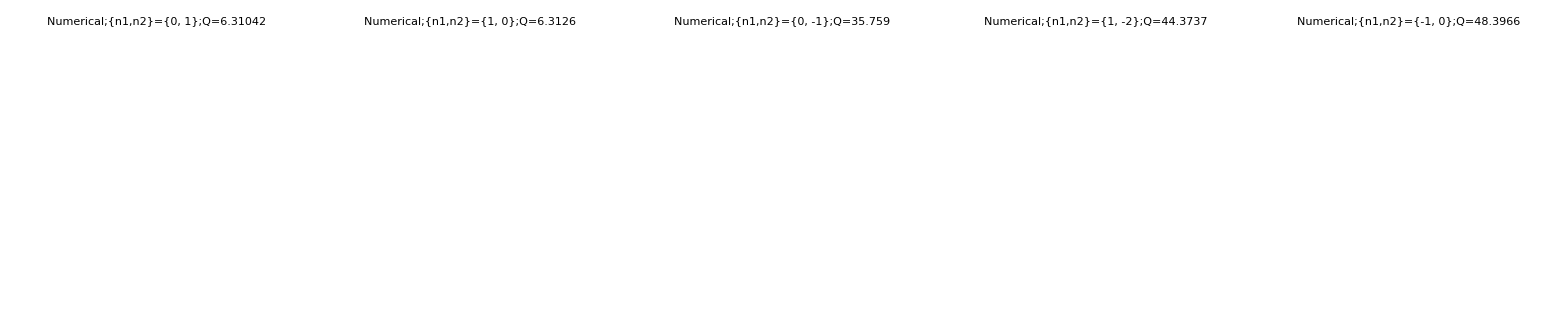
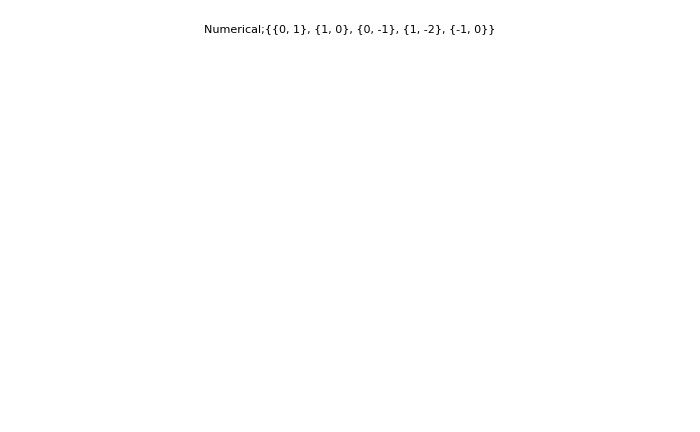

```mathematica
Module[{k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,listOfn1n2},
k1M=k1V;
k2M=k2V;
k3M=k3V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
a3M=a3V;
thetamM=thetamV;
endpointM=endpoint3;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1];*)
(*listOfn1n2={{1,1},{0,1},{1,0},{-1,0},{0,-1}};*)

listOfn1n2=Flatten[Drop[Part[orderedQList[{-3,3},{-3,3},k1M,k2M,a1M,a2M,thetamM],1;;5],None,{2}],1];

Grid[{
{
Grid[{Table[Show[plt3N[k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,Red],plt0n1n2List[{listOfn1n2Table},k1M,k2M,a1M,a2M,thetamM,endpointM,"{n1,n2}="<>ToString[listOfn1n2Table]<>";Q="<>ToString[qDis2Width[listOfn1n2Table[[1]],listOfn1n2Table[[2]],k1M,k2M,a1M,a2M,thetamM]],Blue],PlotRange->All],{listOfn1n2Table,listOfn1n2}]}]
},{
Show[plt3N[k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,Red],plt0n1n2List[listOfn1n2,k1M,k2M,a1M,a2M,thetamM,endpointM,ToString[listOfn1n2],Blue],PlotRange->All]
}}]

]
```

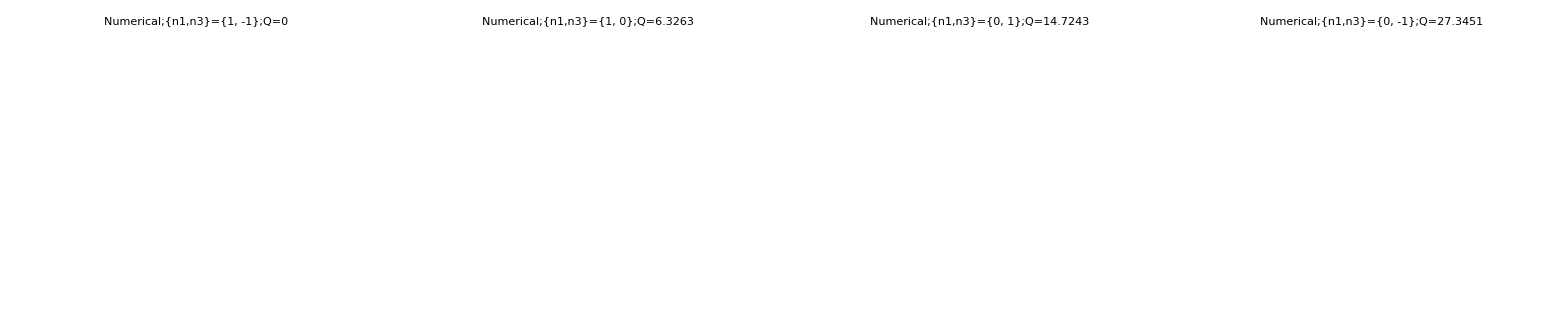
-Graphics-
-Graphics-

```mathematica
Module[{k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,listOfn1n2},
k1M=k1V;
k2M=k2V;
k3M=k3V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
a3M=a3V;
thetamM=thetamV;
endpointM=endpoint3;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1];*)
(*listOfn1n2={{1,1},{0,1},{1,0},{-1,0},{0,-1}};*)

listOfn1n2=Flatten[Drop[Part[orderedQList[{-3,3},{-3,3},k1M,k3M,a1M,a3M,thetamM],1;;4],None,{2}],1];

Grid[{
{
Grid[{Table[Show[plt3N[k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,Red],plt0n1n2List[{listOfn1n2Table},k1M,k3M,a1M,a3M,thetamM,endpointM,"{n1,n3}="<>ToString[listOfn1n2Table]<>";Q="<>ToString[qDis2Width[listOfn1n2Table[[1]],listOfn1n2Table[[2]],k1M,k3M,a1M,a3M,thetamM]],Blue],PlotRange->All],{listOfn1n2Table,listOfn1n2}]}]
},{
Show[plt3N[k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,Red],plt0n1n2List[listOfn1n2,k1M,k3M,a1M,a3M,thetamM,endpointM,ToString[listOfn1n2],Blue],PlotRange->All]
}}]

]
```

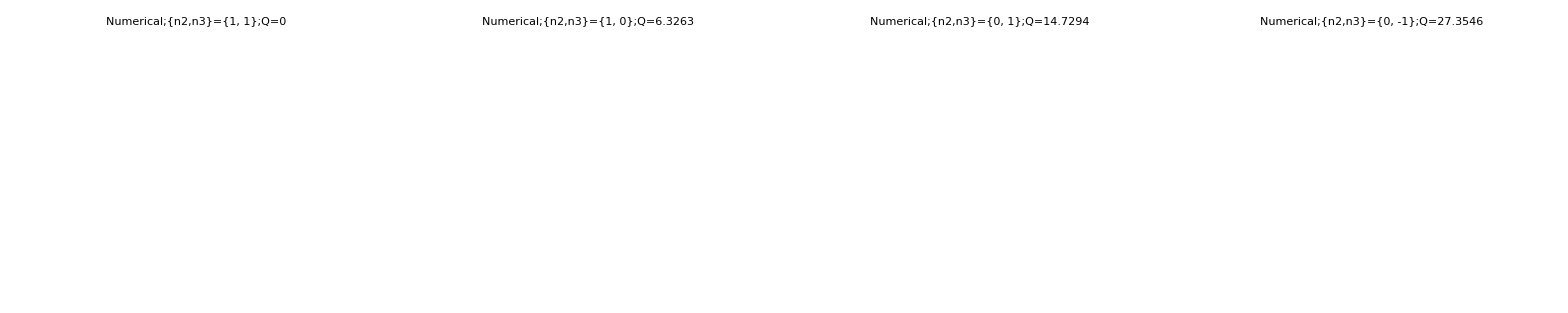
-Graphics-
-Graphics-

```mathematica
Module[{k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,listOfn1n2},
k1M=k1V;
k2M=k2V;
k3M=k3V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
a3M=a3V;
thetamM=thetamV;
endpointM=endpoint3;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1];*)
(*listOfn1n2={{1,1},{0,1},{1,0},{-1,0},{0,-1}};*)

listOfn1n2=Flatten[Drop[Part[orderedQList[{-3,3},{-3,3},k2M,k3M,a2M,a3M,thetamM],1;;4],None,{2}],1];

Grid[{
{
Grid[{Table[Show[plt3N[k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,Red],plt0n1n2List[{listOfn1n2Table},k2M,k3M,a2M,a3M,thetamM,endpointM,"{n2,n3}="<>ToString[listOfn1n2Table]<>";Q="<>ToString[qDis2Width[listOfn1n2Table[[1]],listOfn1n2Table[[2]],k2M,k3M,a2M,a3M,thetamM]],Blue],PlotRange->All],{listOfn1n2Table,listOfn1n2}]}]
},{
Show[plt3N[k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,Red],plt0n1n2List[listOfn1n2,k2M,k3M,a2M,a3M,thetamM,endpointM,ToString[listOfn1n2],Blue],PlotRange->All]
}}]

]
```

```mathematica
bCoef3[n1_,n2_,n3_,k1_,k2_,k3_,a1_,a2_,a3_,thetam_]:=Piecewise[{{
-(-I)^(n1+n2+n3) Tan[2thetam]/2 (n1 k1+n2 k2+n3 k3) BesselJ[n1,a1/k1 Cos[2thetam]]BesselJ[n2,a2/k2 Cos[2thetam]]BesselJ[n3,a3/k3 Cos[2thetam]],k1≠0&&k2≠0
},{
-(-I)^(n1+n2+n3) Tan[2thetam]/2 (n1 k1+n2 k2+n3 k3) BesselJ[n1,Infinity]BesselJ[n2,a2/k2 Cos[2thetam]]BesselJ[n3,a3/k3 Cos[2thetam]],k1==0||k2≠0
},{
-(-I)^(n1+n2+n3) Tan[2thetam]/2 (n1 k1+n2 k2+n3 k3)BesselJ[n1,a1/k1 Cos[2thetam]]BesselJ[n2,Infinity]BesselJ[n3,a3/k3 Cos[2thetam]],k1≠0||k2==0
}}];

hamiltonian03[n1_,n2_,n3_,k1_,k2_,k3_,a1_,a2_,a3_,thetam_]:=(bCoef3[n1,n2,n3,k1,k2,k3,a1,a2,a3,thetam])*Exp[I(n1*phi1V+n2*phi2V+n3*phi3V)]*Exp[I(n1*k1+n2*k2+n3*k3-1)x];
```

```mathematica
sol3List[listInput_,k1_,k2_,k3_,a1_,a2_,a3_,thetam_,endpoint_]:=Module[{k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,listInputM,hamil,b3},
k1M=k1V;
k2M=k2V;
k3M=k3V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
a3M=a3V;
thetamM=thetamV;
endpointM=endpoint;

(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1];*)
(*listOfn1n2={{1,1},{0,1},{1,0},{-1,0},{0,-1}};*)
listInputM=listInput;


hamil=Total@Table[hamiltonian03[NlistM[[1]],NlistM[[2]],NlistM[[3]],k1M,k2M,k3M,a1M,a2M,a3M,thetamM],{NlistM,listInputM}];
NDSolve[I D[{psi1[x],psi2[x]},x]=={{0,hamil},{Conjugate[hamil],0}}.{psi1[x],psi2[x]}&&init,{psi1,psi2},{x,0,endpoint}]

]
```

```mathematica
sol3List[{{1,1,1}},k1V,k2V,k3V,a1V,a2V,a3V,thetamV,endpoint3]
```

{{psi1→InterpolatingFunction[{{0., 400.}}, <>],psi2→InterpolatingFunction[{{0., 400.}}, <>]}}

```mathematica
plt3List[listInput_,k1_,k2_,k3_,a1_,a2_,a3_,thetam_,endpoint_,legends_,color_]:=Plot[Evaluate[Abs[psi2[x]]^2/.sol3List[listInput,k1,k2,k3,a1,a2,a3,thetam,endpoint]],{x,0,endpoint},ImageSize->imgsize,Frame->True,FrameLabel->{"x","Transition Probability"},PlotStyle->color,PlotLegends->Placed[Style[ToString[legends],color],{Top,Center}]]
```

```mathematica
list3GeneratorTest[n1Range_,n2Range_,n3Range_]:=Module[{},
Flatten[Table[{n1,n2,n3},{n1,n1Range[[1]],n1Range[[2]]},{n2,n2Range[[1]],n2Range[[2]]},{n3,n3Range[[1]],n3Range[[2]]}],2]
]
```

```mathematica
list3GeneratorTest[{-1,1},{-1,1},{-1,1}]
```

{{-1,-1,-1},{-1,-1,0},{-1,-1,1},{-1,0,-1},{-1,0,0},{-1,0,1},{-1,1,-1},{-1,1,0},{-1,1,1},{0,-1,-1},{0,-1,0},{0,-1,1},{0,0,-1},{0,0,0},{0,0,1},{0,1,-1},{0,1,0},{0,1,1},{1,-1,-1},{1,-1,0},{1,-1,1},{1,0,-1},{1,0,0},{1,0,1},{1,1,-1},{1,1,0},{1,1,1}}

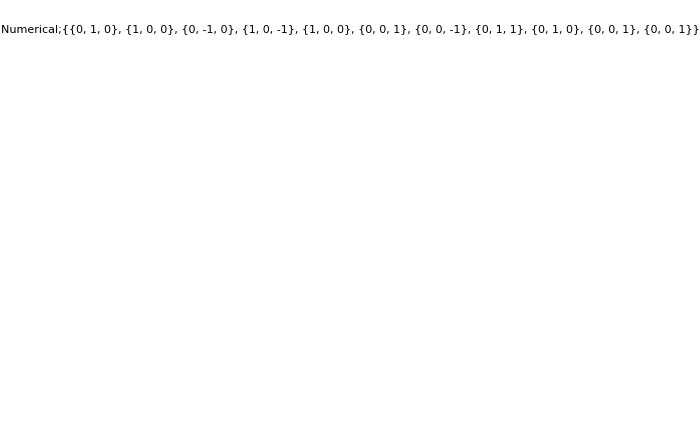

```mathematica
Module[{k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,inputListM,listRangeM},
k1M=k1V;
k2M=k2V;
k3M=k3V;
a1M=a1V;(*0.1(k1A)^(-5/3);*)
a2M=a2V;(*(k2A)^(-5/3);*)
a3M=a3V;
thetamM=thetamV;
endpointM=endpoint3;
(*listOfn1n2=Flatten[Table[{n1M,n2M},{n1M,-1,1},{n2M,-1,1}],1];*)
(*listOfn1n2={{1,1},{0,1},{1,0},{-1,0},{0,-1}};*)

listRangeM={-1,1};
(*inputListM=list3GeneratorTest[listRangeM,listRangeM,listRangeM];*)

inputListM=Flatten[{{{0,1,0},{1,0,0},{0,-1,0}},{{1,0,-1},{1,0,0},{0,0,1},{0,0,-1}},{{0,1,1},{0,1,0},{0,0,1},{0,0,1}}},1];

Show[plt3N[k1M,k2M,k3M,a1M,a2M,a3M,thetamM,endpointM,Red],plt3List[inputListM,k1V,k2V,k3V,a1V,a2V,a3V,thetamV,endpoint3,ToString[inputListM],Blue],PlotRange->All]


]
```

A comment
Removing the {0,0,1} from the last part of the input list will make a huge difference, even though it plays a tiny role in the n1=0 case.